```mathematica
SetDirectory[NotebookDirectory[]];
```

# h_scaling

## data

```mathematica
mpi=Flatten[Import["./mpi/buffer/mPion.dat"]];
```

```mathematica
fpi=Flatten[Import["./mub0/buffer/fpi.dat"]];
h=Flatten[Import["./mub0/buffer/c.dat"]]*197.33^3;
datamub0=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub0=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub0linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];

fpi=Flatten[Import["./mub50/buffer/fpi.dat"]];
h=Flatten[Import["./mub50/buffer/c.dat"]]*197.33^3;
data=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub50=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub50linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];

fpi=Flatten[Import["./mub100/buffer/fpi.dat"]];
h=Flatten[Import["./mub100/buffer/c.dat"]]*197.33^3;
data=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub100=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub100linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];

fpi=Flatten[Import["./mub150/buffer/fpi.dat"]];
h=Flatten[Import["./mub150/buffer/c.dat"]]*197.33^3;
data=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub150=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub150linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];

fpi=Flatten[Import["./mub200/buffer/fpi.dat"]];
h=Flatten[Import["./mub200/buffer/c.dat"]]*197.33^3;
data=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub200=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub200linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];


fpi=Flatten[Import["./mub250/buffer/fpi.dat"]];
h=Flatten[Import["./mub250/buffer/c.dat"]]*197.33^3;
data=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub250=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub250linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];


fpi=Flatten[Import["./mub300/buffer/fpi.dat"]];
h=Flatten[Import["./mub300/buffer/c.dat"]]*197.33^3;
datamub300=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub300=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub300linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];

fpi=Flatten[Import["./mub350/buffer/fpi.dat"]];
h=Flatten[Import["./mub350/buffer/c.dat"]]*197.33^3;
data=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub350=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub350linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];


fpi=Flatten[Import["./mub400/buffer/fpi.dat"]];
h=Flatten[Import["./mub400/buffer/c.dat"]]*197.33^3;
datamub400=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub400=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub400linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];

fpi=Flatten[Import["./mub450/buffer/fpi.dat"]];
h=Flatten[Import["./mub450/buffer/c.dat"]]*197.33^3;
data=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub450=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub450linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];


fpi=Flatten[Import["./mub500/buffer/fpi.dat"]];
h=Flatten[Import["./mub500/buffer/c.dat"]]*197.33^3;
datamub500=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub500=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub500linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];

fpi=Flatten[Import["./mub550/buffer/fpi.dat"]];
h=Flatten[Import["./mub550/buffer/c.dat"]]*197.33^3;
datamub550=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub550=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub550[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub550linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub550[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];

fpi=Flatten[Import["./mub575/buffer/fpi.dat"]];
h=Flatten[Import["./mub575/buffer/c.dat"]]*197.33^3;
datamub575=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub575=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub575[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub575linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub575[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];

fpi=Flatten[Import["./mub600/buffer/fpi.dat"]];
h=Flatten[Import["./mub600/buffer/c.dat"]]*197.33^3;
datamub600=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub600=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub600linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
```

## Plot

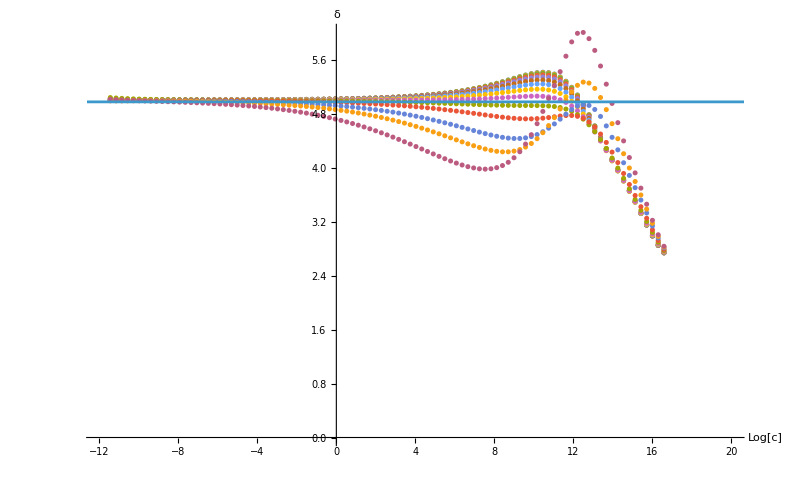

```mathematica
ploth=Show[ListPlot[{h1mub0,h1mub50,h1mub100,h1mub150,h1mub200,h1mub250,h1mub300,h1mub350,h1mub400,h1mub450,h1mub500,h1mub550,h1mub575,h1mub600},AxesLabel->{"Log[c]","δ"},PlotLegends->{(*"μ_B=0","μ_B=50MeV","μ_B=100MeV","μ_B=150MeV","μ_B=200MeV","μ_B=250MeV","μ_B=300MeV","μ_B=350MeV",*)(*"μ_B=400MeV","μ_B=450MeV","μ_B=500MeV","μ_B=550MeV"*)(*,"μ_B=600MeV","μ_B=650MeV","μ_B=700MeV"*)},Axes->True,PlotRange->{{-12,20},All}],ListLinePlot[{{-20,4.975},{100,4.975}}]]
```

```mathematica
Export["./LOdata/mub0.dat",h1mub0linear];
Export["./LOdata/mub50.dat",h1mub50linear];
Export["./LOdata/mub100.dat",h1mub100linear];
Export["./LOdata/mub150.dat",h1mub150linear];
Export["./LOdata/mub200.dat",h1mub200linear];
Export["./LOdata/mub250.dat",h1mub250linear];
Export["./LOdata/mub300.dat",h1mub300linear];
Export["./LOdata/mub350.dat",h1mub350linear];
Export["./LOdata/mub400.dat",h1mub400linear];
Export["./LOdata/mub450.dat",h1mub450linear];
Export["./LOdata/mub500.dat",h1mub500linear];
Export["./LOdata/mub550.dat",h1mub550linear];
Export["./LOdata/mub575.dat",h1mub575linear];
Export["./LOdata/mub600.dat",h1mub600linear];
```